```mathematica
Norm[1+Exp[-0.5*I]]^2/2
```

1.87758

```mathematica
1+Cos[1]
```

1+Cos[1]

```mathematica
N[1+Cos[0.5]]
```

1.87758

```mathematica
data=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",2}];
```

```mathematica
Dimensions[data]
```

{801,25}

## 2D square lattice

```mathematica
lattice2D = data[[All,1;;6]];
```

```mathematica
square100 = lattice2D[[All,{1,2}]];
```

```mathematica
square400 = lattice2D[[All,{1,3}]];
```

```mathematica
square625 = lattice2D[[All,{1,4}]];
```

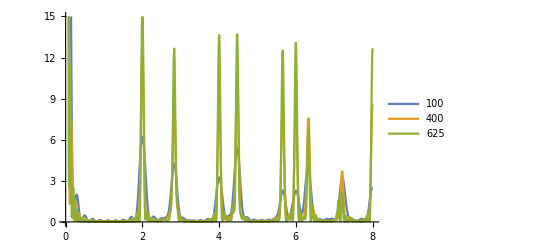

```mathematica
ListLinePlot[{square100,square400,square625},PlotRange->{0,15},PlotLegends->{"100","400","625"}]
```

```mathematica
sqcsv = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\squareLattice2D900.csv",{"Data"}]
```

{{0.,0.,900.},{0.,0.05,81.2238},{0.,0.1,40.8635},{0.,0.15,9.17486},{0.,0.2,1.76509×10^-30},{0.,0.25,3.41421},14630,{6.,5.8,6.54158×10^-26},{6.,5.85,9.17486},{6.,5.9,40.8635},{6.,5.95,81.2238},{6.,6.,900.}}
 |  |  |  |

```mathematica
ListPlot3D[sqcsv,PlotRange->{0,100}]
```

-Graphics3D-

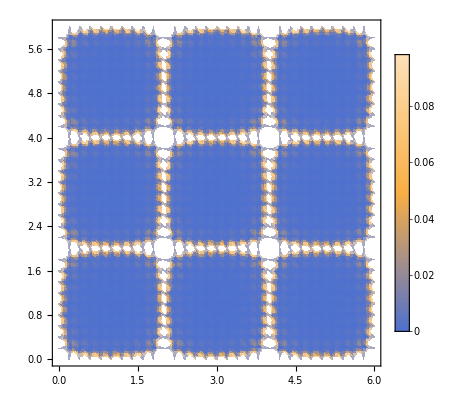

```mathematica
ListDensityPlot[sqcsv,PlotTheme->"Business"]
```

## 2D triangle lattice

```mathematica
triangle2D = data[[All,13;;21]];
```

```mathematica
triang100=triangle2D[[All,{1,2}]];
triang400 = triangle2D[[All,{1,3}]];
triang900 = triangle2D[[All,{1,4}]];
triang3600 = triangle2D[[All,{8,9}]];
```

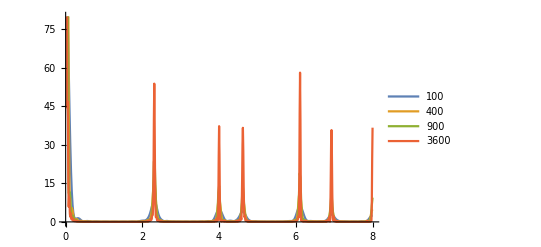

```mathematica
ListLinePlot[{triang100,triang400,triang900,triang3600},PlotRange->{0,80},PlotLegends->{"100","400","900","3600"}]
```

```mathematica
N[12/(Sqrt[3])]
```

6.9282

```mathematica
triangcsv = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\triangleLattice2D900.csv",{"Data"}]
```

{{0.,0.,900.},{0.,0.05,172.131},{0.,0.1,35.4309},{0.,0.15,0.630547},{0.,0.2,12.5743},{0.,0.25,4.42574},25910,{8.,7.8,0.846177},{8.,7.85,0.00709727},{8.,7.9,0.910988},{8.,7.95,0.592818},{8.,8.,0.0580487}}
 |  |  |  |

```mathematica
ListPlot3D[triangcsv,PlotRange->{0,100}]
```

-Graphics3D-

```mathematica
ListDensityPlot[triangcsv,Mesh->All,MeshFunctions->Automatic]
```

-Graphics-

## 2D ideal gas

```mathematica
ideal2D = data[[All,7;;11]];
```

```mathematica
ideal100 = ideal2D[[All,{1,2}]];
```

```mathematica
ideal225 = ideal2D[[All,{1,3}]];
```

```mathematica
ideal400 = ideal2D[[All,{1,4}]];
```

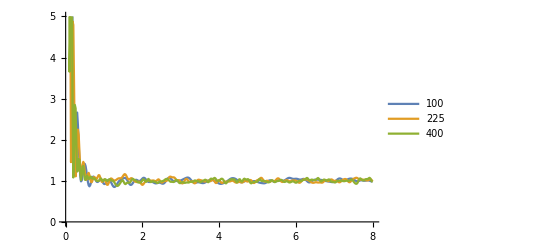

```mathematica
ListLinePlot[{ideal100,ideal225,ideal400},PlotRange->{0,5},PlotLegends->{"100","225","400"}]
```

## 1D lattice

```mathematica
data1D=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",1}];
```

```mathematica
lat1D = data1D[[All,1;;5]];
```

```mathematica
lat1D5 = lat1D[[All,{1,2}]];
lat1D10 = lat1D[[All,{1,3}]];
```

```mathematica
lat1D20 = lat1D[[All,{1,4}]];
```

```mathematica
lat1D40 = lat1D[[All,{1,5}]];
```

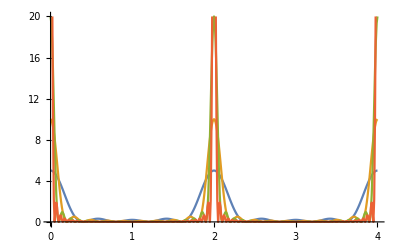

```mathematica
ListLinePlot[{lat1D5,lat1D10,lat1D20,lat1D40},PlotRange->{0,20}]
```

```mathematica
S[k_,n_]:=Norm[Sum[Exp[-I*k*(j/n)],{j,0,n-1}]]^2/n
```

```mathematica
S[3,10]
```

1/10 ((1+Cos[3/10]+Cos[3/5]+Cos[9/10]+Cos[6/5]+Cos[3/2]+Cos[9/5]+Cos[21/10]+Cos[12/5]+Cos[27/10])^2+(-Sin[3/10]-Sin[3/5]-Sin[9/10]-Sin[6/5]-Sin[3/2]-Sin[9/5]-Sin[21/10]-Sin[12/5]-Sin[27/10])^2)

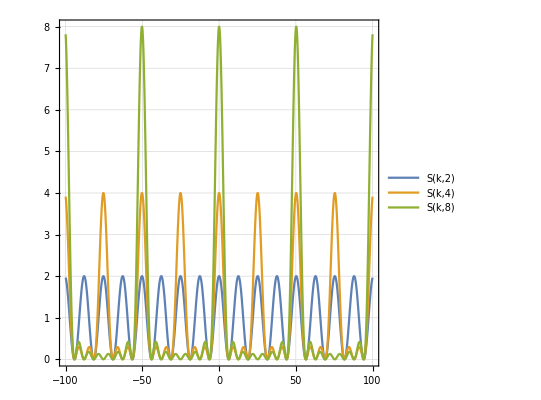

```mathematica
Plot[{S[k,2],S[k,4],S[k,8]},{k,-100,100},PlotRange->{0,8},AspectRatio->1,PlotTheme->"Detailed"]
```

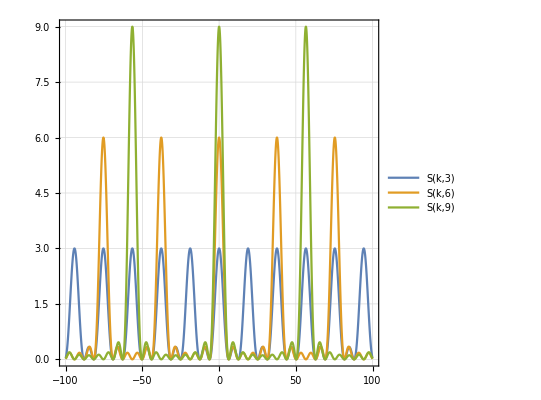

```mathematica
Plot[{S[k,3],S[k,6],S[k,9]},{k,-100,100},PlotRange->{0,9},AspectRatio->1,PlotTheme->"Detailed"]
```

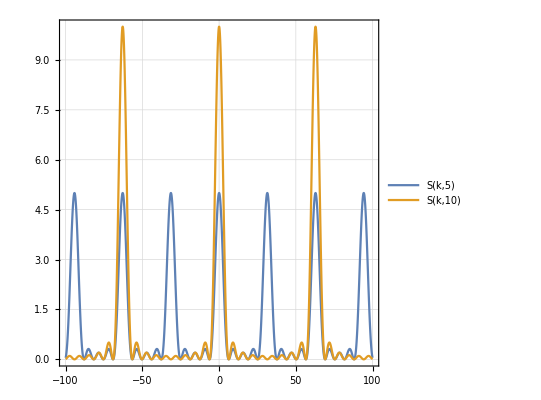

```mathematica
Plot[{S[k,5],S[k,10]},{k,-100,100},PlotRange->{0,10},AspectRatio->1,PlotTheme->"Detailed"]
```

## 1D ideal gas

```mathematica
gas1D = data1D[[All,6;;10]];
```

```mathematica
gas1D5 = gas1D[[All,{1,2}]];
gas1D10 = gas1D[[All,{1,3}]];
```

```mathematica
gas1D40 = gas1D[[All,{1,4}]];
```

```mathematica
gas1D160 = gas1D[[All,{1,5}]];
```

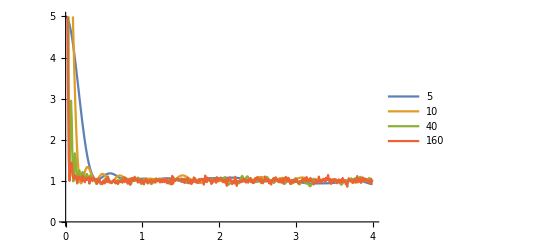

```mathematica
ListLinePlot[{gas1D5,gas1D10,gas1D40,gas1D160},PlotRange->{0,5},PlotLegends->{"5","10","40","160"}]
```

## Moving to 3D: uniformly sample the surface of a unit sphere

```mathematica
sphereUniform = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\sphereUniform.csv",{"Data"}];
```

```mathematica
ListPointPlot3D[sphereUniform,PlotStyle->RGBColor[0.89,0.51,0.],BoxRatios->{1,1,1}]
```

-Graphics3D-

## 3D equilibrium hard sphere

Assuming D = 1.

```mathematica
a1[ϕ_]:=(1+2 ϕ)^2/(1-ϕ)^4
```

```mathematica
a2[ϕ_]:=-(1+ϕ/2)^2/(1-ϕ)^4
```

```mathematica
c[q_,ϕ_]:=-4*Pi/q^3(a1[ϕ]*(Sin[q]-q*Cos[q])+6*ϕ*a2[ϕ]/q*(2*q*Sin[q]+(2-q^2)*Cos[q]-2)+ϕ*a1[ϕ]/(2*q^3)*(4*q*(q^2-6)*Sin[q]-(24-12*q^2+q^4)*Cos[q]+24))
```

```mathematica
ρ[ϕ_]:=6*ϕ/Pi
```

```mathematica
hTilda[k_,ϕ_]:=c[k,ϕ]/(1-ρ[ϕ]*c[k,ϕ])
```

```mathematica
S3d[k_,ϕ_]:=hTilda[k,ϕ]*ρ[ϕ]+1
```

```mathematica
S3d[2*Pi,0.2]
```

1.23654

```mathematica
S3d[4*Pi,0.2]
```

1.05389

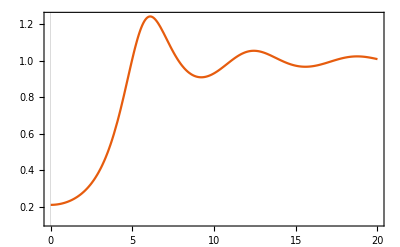

```mathematica
theory=Plot[S3d[x,0.2],{x,0,20},PlotRange->All,PlotTheme->Scientific]
```

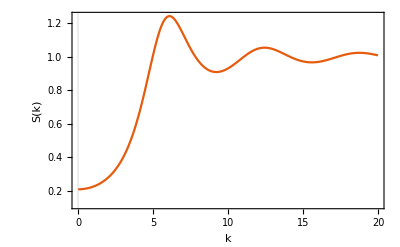

```mathematica
Show[%41,FrameLabel->{{HoldForm["S(k)"],None},{HoldForm[k],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
data3D=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",3}];
```

```mathematica
skHardSphere = data3D[[All,{1,2}]];
```

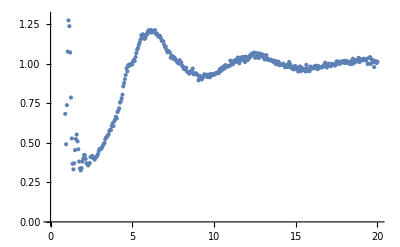

```mathematica
simu=ListPlot[skHardSphere,PlotRange->{0,1.3}]
```

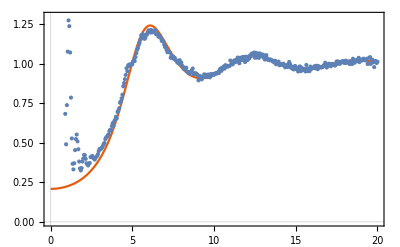

```mathematica
Show[theory,simu,PlotRange->{0,1.3}]
```